# MATHEMATICA : PRÁCTICA 1

Primera Parte

1.- Desarrollar un sistema generador de números aleatorios basado en un generador lineal congruencial mixto que siga una distribución uniforme entre [0,1].

```mathematica
(* Generador congruencial mixto: c distinto de 0 *)
```

```mathematica
(* Damos un valor aleatorio a Zn y el resto de parámetros toman los valores típicos del método Kobayashi *)
(* FÓRMULA: Zi = (a*Zi+c)mod(m) *)
```

```mathematica
Module[{zn=78955773,a=314159269,c=453806245,m=2^31},RandomData[]:=(zn=Mod[a*zn+c,m])/(m-1)//N
]
```

```mathematica
(* Dividimos entre (m-1) para que los valores nos queden entre 0-1 *)
```

```mathematica
RandomData[]
```

0.12361

```mathematica
(* Creamos el Histograma *)
```

```mathematica
numMuestras=10000;
```

2.- Probar el generador y demostrar mediante un hisograma la bondad del generador

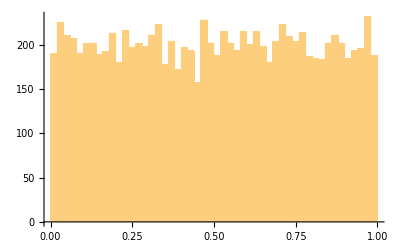

```mathematica
Histogram[Table[RandomData[],{numMuestras}],50]
```

3.- Implementar el método de transformada inversa para obtener una distribución aleatoria exponencial de tiempo entre llegadas 1/landa. Representar en un histograma los valores obtenidos.

```mathematica
(* Método de Transformada Inversa: -1/landa*ln(u) *)
(* Siendo u una variable aleatoria de distribución uniforme *)
```

```mathematica
RandomExp[Landa_]:=-1/Landa*Log[RandomData[]]
```

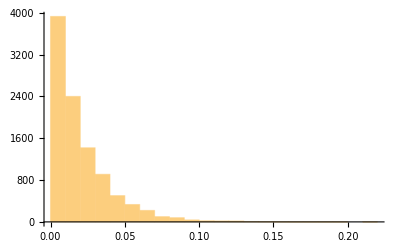

```mathematica
Histogram[Table[RandomExp[50],{numMuestras}]]
```

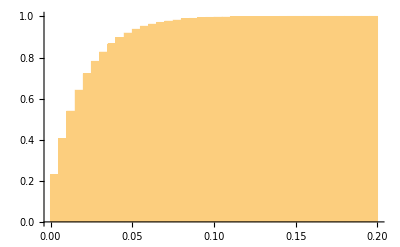

```mathematica
Histogram[Table[RandomExp[50],{numMuestras}],50,CDF]
```

Segunda Parte

4.- Desarrollar un simulador de una cola M/M/1 con tasa Landa de llegados y Mu de servicio. Representar en un diagrama que evolucione en el tiempo el número de usuarios en el sistema.

```mathematica
nmax=1000;
```

```mathematica
(* Tomamos valores aleatorios de los parámetros Landa (tiempo entre llegadas) y Mu (tiempo de servicio) *)
```

```mathematica
landa=100;
```

```mathematica
mu=130;
```

```mathematica
(* El tiempo real entre llegadas es exponencial *)
```

```mathematica
(* Almacenamos los valores aleatorios correspondientes al tiempo entre llegadas de una distribución poissoniana en una lista *)
```

```mathematica
InterArrivalsTime[landa_]:= Table[RandomExp[landa],{nmax}]//N;
```

```mathematica
tiemposEntreLlegadas=InterArrivalsTime[landa];
```

```mathematica
(* Almacenamos en otra lista los valores correspondientes a los tiempos de servicio de los paquetes *)
```

```mathematica
ServiceTimes[mu_]:=Table[RandomExp[mu],{nmax}]//N;
```

```mathematica
tiemposDeServicio=ServiceTimes[mu];
```

```mathematica
(* A continuación se crea una función que permita calcular con los tiempo de la lista InterArrivals los tiempos definitivos a partir de un origen de tiempo 0 *)
```

```mathematica
Module[{t=0},
AcumSeries[tiemposEntreLlegadas_]:=Map[(t += #)&,tiemposEntreLlegadas]];
```

```mathematica
tiemposDeLlegadas=AcumSeries[tiemposEntreLlegadas];
```

```mathematica
(* Construir una lista de tiempos de salida en función de los tiemposDeLlegadas y los tiemposDeServicio *)
```

```mathematica
(* Para ello hacemos una función que recoja para cada paquete que entra en el sistema cuándo le corresponde ser atendido. Si seguimos una política FIFO, cuando un paquete es servido corresponderá al siguiente de la lista de salida *)
```

```mathematica
(* Variable n: nos indica el paquete en el que nos encontramos *)
```

```mathematica
(* Variable checkTime: nos indica el instante de tiempo en el que estamos observando (lo inicializamos en el tiempo del primer evento) *)
```

```mathematica
(* La función Map nos indica el tiempo de salida de cada paquete. El '&' lo ponemos para que la ecuación de Map se ejecute para cada tiempo de llegada *)
```

```mathematica
(* Función If: comprueba si el tiempo de llegada es mayor o igual a #. 
Si es igual, el tiempo de salida será igual a la suma del tiempo de servicio más el tiempo de chequeo, el paquete se sitúa en el checkTime donde nos encontramos y se incrementa n para situarnos en el siguiente paquete. 
Si el checkTime es menor, el tiempo de salida será igual al tiempo de llegada más el tiempo de servicio y volvemos a incrementar n *)
```

```mathematica
FifoSchedulling[arrivals_,service_]:=
Module[{n,checkTime},
n=1;checkTime=arrivals[[1]];
Map[(If[checkTime≥#,checkTime+=service[[n++]],
checkTime=#+service[[n++]]])&,arrivals]
]
```

```mathematica
(* Lista de tiempos de salida de los paquetes en el servidor *)
```

```mathematica
DeparturesTime=FifoSchedulling[tiemposDeLlegadas,tiemposDeServicio];
```

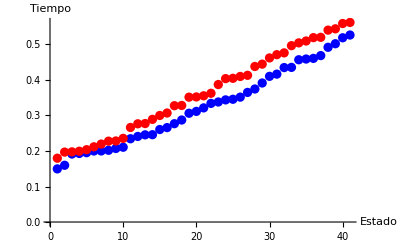

```mathematica
ListPlot[{tiemposDeLlegadas[[20;;60]],DeparturesTime[[20;;60]]},PlotStyle->{Blue,Red},AxesLabel->{"Estado","Tiempo"}]
```

```mathematica
(* El problema es que en esta gráfica los ejes aparecen girados: en el eje x aparece el valor de N y en el eje y el valor del tiempo *)
```

```mathematica
(* Para mejorarlo, tenemos que cambiar la lista de tiempos por una lista de coordenadas, para poder obtener la gráfica en forma de escalera *)
```

```mathematica
(* Para dibujar los escalones, por cada tiempo de llegada tenemos que dibujar dos puntos: uno en el escalón que corresponda y el otro en un escalón superior, para que después, al unir todos los puntos podamos ver representada la gráfica escalonada *)
```

```mathematica
PointsStairStep[arrivalsTime_]:=
Module[{e=0},Flatten[Map[({{ #,e},{#,e+=1}})&,arrivalsTime],1]
]
```

```mathematica
arrivalsStairStep=PointsStairStep[tiemposDeLlegadas];
```

```mathematica
departuresStairStep=PointsStairStep[DeparturesTime];
```

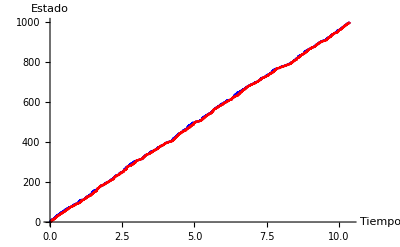

```mathematica
ListLinePlot[{arrivalsStairStep,departuresStairStep},PlotStyle->{Blue,Red},AxesLabel->{"Tiempo","Estado"}]
```

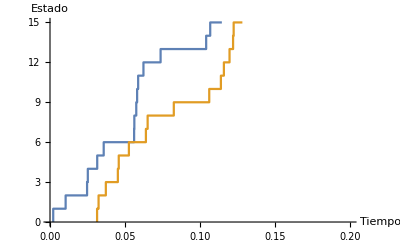

```mathematica
ListLinePlot[{arrivalsStairStep,departuresStairStep},PlotRange->{{0,0.2},{0,15}},AxesLabel->{"Tiempo","Estado"}]
```

```mathematica
(* Para visualizarlo mejor vamos a crear un efecto zoom y de desplazamiento *)
```

```mathematica
(* Creamos un punto de origen: origen {0,nmax} y un ancho de muestras: with {minwin,maxwin} *)
```

```mathematica
minwin=10;
```

```mathematica
maxwin=100;
```

```mathematica
Manipulate[ListPlot[{arrivalsStairStep[[origen;;origen+with]],departuresStairStep[[origen;;origen+with]]},
PlotStyle->{Blue,Red},AxesLabel->{"Tiempo","Estado"}],{origen,1,nmax,1},
{with,minwin,maxwin,1}]
```

Part::take: Cannot take positions 1 through 11 in arrivalsStairStep.

Part::take: Cannot take positions 1 through 11 in departuresStairStep.

Part::take: Cannot take positions 1 through 11 in arrivalsStairStep.

Part::take: Cannot take positions 1 through 11 in departuresStairStep.

Part::take: Cannot take positions 1 through 11 in arrivalsStairStep.

Part::take: Cannot take positions 1 through 11 in departuresStairStep.

```mathematica
(* Ahora creamos una gráfica escalonada *)
```

```mathematica
Manipulate[
ListLinePlot[{arrivalsStairStep[[origen;;origen+with]],
departuresStairStep[[origen;;origen+with]]},
PlotStyle->{Blue,Red},AxesLabel->{"Tiempo","Estado"}],{origen,1,nmax,1},
{with,minwin,maxwin,1}]
```

Part::take: Cannot take positions 1 through 11 in arrivalsStairStep.

Part::take: Cannot take positions 1 through 11 in departuresStairStep.

Part::take: Cannot take positions 1 through 11 in arrivalsStairStep.

Part::take: Cannot take positions 1 through 11 in departuresStairStep.

```mathematica
(* Algo importante sería representar la evolución de N(t). Esto nos daría el número de usuarios en el sistema a cada instante *)
```

```mathematica
(* Para ello vamos a crear la lista UsersStepStairs que nos de la evolución y el estado entre cada suceso *)
```

```mathematica
(* Los paquetes de llegada van a tener la siguiente forma : {tllegada,1} *)
```

```mathematica
Llegadas[arrivals_]:=Map[{#,1}&,arrivals];
```

```mathematica
Llegadas[tiemposDeLlegadas[[10;;20]]]
```

{{0.0580802,1},{0.0587661,1},{0.0622985,1},{0.0737264,1},{0.104108,1},{0.106808,1},{0.11457,1},{0.130135,1},{0.13862,1},{0.14207,1},{0.149664,1}}

```mathematica
(* Los paquetes de salida van a tener la siguiente forma : {tsalida,-1} *)
```

```mathematica
Salidas[departures_]:=Map[{#,-1}&,departures];
```

```mathematica
Salidas[DeparturesTime[[10;;20]]]
```

{{0.10616,-1},{0.113932,-1},{0.115924,-1},{0.11969,-1},{0.12205,-1},{0.122439,-1},{0.128247,-1},{0.153345,-1},{0.164354,-1},{0.177127,-1},{0.179721,-1}}

```mathematica
(* Unimos todos los paquetes anteriores en una fila por orden de tiempo *)
```

```mathematica
Events=Union[Llegadas[tiemposDeLlegadas],Salidas[DeparturesTime]];
```

```mathematica
Events[[10;;20]]
```

{{0.0452357,-1},{0.0458352,-1},{0.0525949,-1},{0.0560801,1},{0.0562218,1},{0.0575097,1},{0.0580802,1},{0.0587661,1},{0.0622985,1},{0.0639359,-1},{0.0650901,-1}}

```mathematica
(*UsersStepStairs[arrivalsTime_,departuresTime_]:=
Module[{e=0,na=1,nd=1},
MapThread[If[arrivalsTime[[na]]<=departuresTime[[nd]],{arrivalsTime[[na++]],e+=1},{departuresTime[[nd++]],e-=1}]&,{arrivalsTime,departuresTime}]];*)
```

```mathematica
UsersStepStairs[Events_]:=Module[{n=0},Map[{#[[1]],n+=#[[2]]}&,Events]];
```

```mathematica
Nt=UsersStepStairs[Events];
```

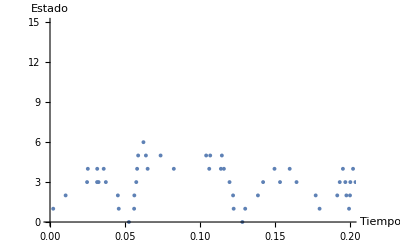

```mathematica
ListPlot[Nt,PlotRange->{{0,0.2},{0,15}},AxesLabel->{"Tiempo","Estado"}]
```

```mathematica
(* Unimos los puntos anteriores *)
```

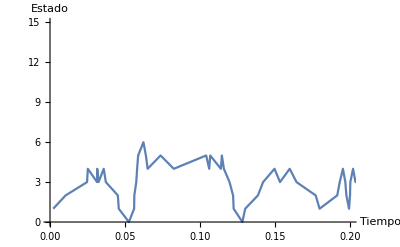

```mathematica
ListLinePlot[Nt,PlotRange->{{0,0.2},{0,15}},AxesLabel->{"Tiempo","Estado"}]
```

```mathematica
(* Tenemos que conseguir que la gráfica aparezca representada mediante escalones *)
```

```mathematica
NtSteps[userStepStairs_]:=Module[{steps={{userStepStairs[[1,1]],0}}},For[i=1,i<Length[userStepStairs],i++,
AppendTo[steps,userStepStairs[[i]]];
AppendTo[steps,{userStepStairs[[i+1,1]],userStepStairs[[i,2]]}]];
steps]
```

```mathematica
(* Primero añadimos una coordenada que tiene el mismo tiempo que el primer paquete anterior y estado 0 *)
(* Después añadimos las coordenadas del paquete que toque *)
(* Por último añadimos las coordenadas en las que el primer término corresponde al tiempo del paquete siguiente y el segundo al del estado del paquete que acabamos de insertar *)
(* Los dos últimos puntos se van repitiendo en forma de bucle hasta llegar a la largura de la lista de UserStepStairs *)
```

```mathematica
NSteps=NtSteps[Nt];
```

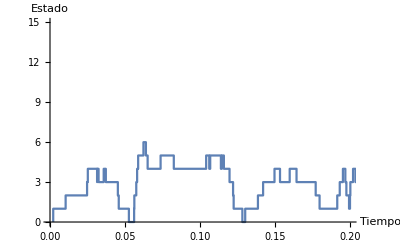

```mathematica
ListLinePlot[NSteps,PlotRange->{{0,0.2},{0,15}},AxesLabel->{"Tiempo","Estado"}]
```

5.- Representar el tiempo medio de espera en el sistema normalizado por mu para diferentes valores de ro. Hacerlo con la curva teórica y representar los puntos obtenidos en las simulaciones.

```mathematica
(* Las muestras de tiempo de retraso de cada paquete se consiguen restando DepartureTime -ArrivalTime. Para obtener la curva hay que sumar todos esos tiempos y calcular la media *)
```

```mathematica
(* CURVA TEÓRICA *)
```

```mathematica
(* Tiempo medio de espera total del sistema según la intensidad de tráfico (depende de ro) *)
```

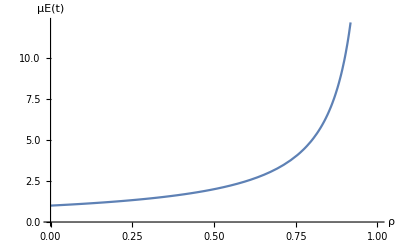

```mathematica
TiempoMedioEspera=Plot[1/(1-ro),{ro,0,1},AxesOrigin->{0,0},AxesLabel->{"ρ","μE(t)"}]
```

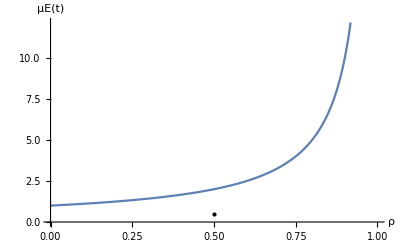

```mathematica
Show[TiempoMedioEspera,Graphics[Point[{0.5,0.5}]]]
```

```mathematica
(* Calculamos el tiempo medio de espera total del sistema E(t) *)
```

```mathematica
GetMeanTime[arrivals_,departures_]:=Mean[MapThread[(#2-#1)&,{arrivals,departures}]];
```

```mathematica
(* La función Mean suma todas las restas (#2-#1) y saca la media de la suma total *)
```

```mathematica
meanTimeTotal=GetMeanTime[tiemposDeLlegadas,DeparturesTime]
```

0.0259684

```mathematica
(* Para adecuarlo con el eje y, tenemos que multiplicar el valor obtenido poor mu *)
```

```mathematica
meanTimeTotal*mu
```

3.37589

```mathematica
(* Representamos la gráfica anterior mediante puntos: tenemos que calcular para cada valor de landa y mu los tiemposDeLlegadas, tiemposDeServicio y departuresTime y en base a ellos calcular el tiempo medio de espera del sistema. Esto nos dará un punto de la gráfica y si lo vamos haciendo con más valores iremos obteniendo el resto de puntos que si los unimos se asemejarán a la curva teórica *)
```

```mathematica
TiempoEsperaSim[landa_,mu_]:=Module[{arrivals=AcumSeries[InterArrivalsTime[landa]],
service=ServiceTimes[mu],departures=List[]}, (* creamos una lista nueva porque no podemos inicializar un parámetro con otros parámetros *)
departures=FifoSchedulling[arrivals,service];
GetMeanTime[arrivals,departures]*mu];
```

```mathematica
puntos=Table[TiempoEsperaSim[lamda,mu],{lamda,1,100}]
```

{0.987925,1.01867,0.979978,1.05137,1.00842,1.09222,1.08032,1.09132,1.03261,1.05826,1.08853,1.11894,1.05709,1.15721,1.20425,1.06175,1.17898,1.15123,1.23079,1.12999,1.16525,1.17075,1.11247,1.25358,1.15156,1.41342,1.28732,1.396,1.22735,1.22753,1.24406,1.32933,1.38065,1.41754,1.33162,1.26322,1.57768,1.39262,1.36787,1.47293,1.47053,1.4769,1.65384,1.51697,1.38671,1.52961,1.62722,1.61304,1.68489,1.69386,1.6058,1.8253,1.6159,1.68801,1.75937,1.74677,1.72687,1.69619,2.15643,1.8385,1.86465,2.14368,1.88444,1.87395,2.1419,1.96085,2.59981,1.97037,1.98501,2.53164,1.95698,2.36872,2.18767,2.2686,2.31044,1.98761,2.08804,2.80214,1.88442,2.87105,2.57408,2.75628,2.2689,2.09838,2.21577,3.14608,3.56497,2.97828,4.24846,2.76124,2.96746,3.81669,3.20929,3.7206,3.67736,6.71924,2.76434,4.63697,5.27693,5.01037}

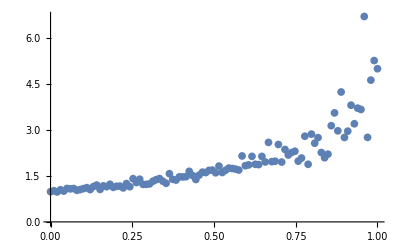

```mathematica
gPuntos=ListPlot[puntos,DataRange->{0,1}]
```

```mathematica
(* Vemos que más o menos los valores teóricos sacados inicialmente coincididen con los puntos del tiempo medio de espera que hemos ido calculando *)
```

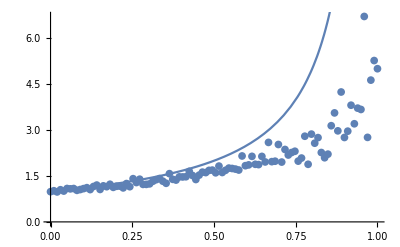

```mathematica
Show[gPuntos,TiempoMedioEspera]
```

```mathematica
Manipulate[Show[
TiempoMedioEspera,
Graphics[{PointSize[Large],Red,
Point[{lamda/mu,
arrivals=AcumSeries[Table[RandomExp[lamda],{nmax}]];
service=Table[RandomExp[mu],{nmax}];
departures=FifoSchedulling[arrivals,service];
GetMeanTime[arrivals,departures]*mu}
]
}
]
],{lamda,1,100}
]
```

Table::iterb: Iterator {nmax} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[TiempoMedioEspera,].

Table::iterb: Iterator {nmax} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[TiempoMedioEspera,].

```mathematica
(* Prueba *)
```

```mathematica
Manipulate[Show[TiempoMedioEspera,Graphics[Point[{ro,2.5}]]],{ro,0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[TiempoMedioEspera,].

Tercera Parte

```mathematica
(* Hacemos muestreo en los tiempo de llegada. Para ello tenemos que inspeccionar el sistema justo antes de los instantes de llegada de los usuarios. Una vez realizado el muestreo sacamos las probabilidades *)
```

6.- Representar las probabilidades de estado pn de la cola M/M/1 teóricas, así como las obtenidas por simulación para diferentes puntos de ensayo. Comprobar si esa distribución coincide con la visualizada según la propiedad PASTA en los tiempos de llega.

```mathematica
(* Enfoque práctico *)
```

```mathematica
(* Hay que sumar los tiempos de permanencia del sistema en cada caso y dividir el resultado entre el tiempo total transcurrido *)
```

```mathematica
(* Hay que filtrar en la línea UsersStepStair los peldaños de la escalera que correspondan al estado n, sumar la longitud de esos peldaños y con el tiempo total calcular para cada n la pn *)
```

```mathematica
(* PASTA *)
```

```mathematica
(* Observar en qué estado n está el sistema justo cuando se produce una llegada *)
```

```mathematica
(* De esta manera se podrá comprobar que la estadística que sale coincide con los estados vistos en los métodos anteriores *)
```

```mathematica
Pasta[arrivals_,departures_]:= Module[{estado=0},{Map[()&,arrivals],Map[()&,departures]}];
```